## Load the package

```mathematica
Get["ProteinStructure.wl"];
```

PDB loaded.

```mathematica
ChangeDirectory[NotebookDirectory[]];
```

## Load one PDB file into PDBDataList

```mathematica
PDBFile = "rs3";
PDBDataList=GetPDB[NotebookDirectory[],PDBFile];
```

84 Residues

```mathematica
84/14(*14 residues in one molecule*)
```

6

```mathematica
PDBDataList (*is a list of "Residue elements".*)(*For each residue element, it's a list of "atom elements".*)(*"atom element" is an association with the information from one line in PDB file*)
```

{{<|AtomNums→1,ElementType→N,AtomNames→N,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.937,-0.238,0.24},SegmentName→|>,<|AtomNums→2,ElementType→H,AtomNames→H1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.648,0.24,-0.293},SegmentName→|>,14,<|AtomNums→17,ElementType→O,AtomNames→O,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.646,-0.919,1.677},SegmentName→|>},82,{<|AtomNums→1394,ElementType→N,5,SegmentName→|>,15,<|1|>}}
 |  |  |  |

```mathematica
Length[PDBDataList]
```

84

```mathematica
PDBDataList[[1]]
```

{<|AtomNums→1,ElementType→N,AtomNames→N,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.937,-0.238,0.24},SegmentName→|>,<|AtomNums→2,ElementType→H,AtomNames→H1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.648,0.24,-0.293},SegmentName→|>,<|AtomNums→3,ElementType→H,AtomNames→H2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.939,-1.236,0.047},SegmentName→|>,<|AtomNums→4,ElementType→H,AtomNames→H3,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.035,-0.1,1.232},SegmentName→|>,<|AtomNums→5,ElementType→C,AtomNames→CA,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.647,0.385,-0.105},SegmentName→|>,<|AtomNums→6,ElementType→H,AtomNames→HA,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.469,0.278,-1.177},SegmentName→|>,<|AtomNums→7,ElementType→C,AtomNames→CB,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.634,1.839,0.353},SegmentName→|>,<|AtomNums→8,ElementType→H,AtomNames→HB1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.574,2.058,0.334},SegmentName→|>,<|AtomNums→9,ElementType→H,AtomNames→HB2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.072,1.877,1.355},SegmentName→|>,<|AtomNums→10,ElementType→C,AtomNames→CG,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.424,2.909,-0.392},SegmentName→|>,<|AtomNums→11,ElementType→H,AtomNames→HG1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.197,2.792,-1.454},SegmentName→|>,<|AtomNums→12,ElementType→H,AtomNames→HG2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.893,3.805,-0.092},SegmentName→|>,<|AtomNums→13,ElementType→C,AtomNames→CD,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.914,2.998,-0.108},SegmentName→|>,<|AtomNums→14,ElementType→O,AtomNames→OE1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-30.616,2.054,-0.538},SegmentName→|>,<|AtomNums→15,ElementType→O,AtomNames→OE2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-30.381,3.94,0.565},SegmentName→|>,<|AtomNums→16,ElementType→C,AtomNames→C,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.497,-0.296,0.625},SegmentName→|>,<|AtomNums→17,ElementType→O,AtomNames→O,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.646,-0.919,1.677},SegmentName→|>}

```mathematica
PDBDataList[[1]][[5]]
```

<|AtomNums→5,ElementType→C,AtomNames→CA,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.647,0.385,-0.105},SegmentName→|>

```mathematica
PDBDataList[[1]][[5]]["AtomCoords"]
```

{-27.647,0.385,-0.105}

```mathematica
MolList=Partition[PDBDataList,14];(*One simple way to group different molecules.*)
Dimensions[MolList]
```

{6,14}

```mathematica
MolList[[1]]
```

{{<|AtomNums→1,ElementType→N,AtomNames→N,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.937,-0.238,0.24},SegmentName→|>,<|AtomNums→2,ElementType→H,AtomNames→H1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.648,0.24,-0.293},SegmentName→|>,<|AtomNums→3,ElementType→H,AtomNames→H2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.939,-1.236,0.047},SegmentName→|>,<|AtomNums→4,ElementType→H,AtomNames→H3,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.035,-0.1,1.232},SegmentName→|>,<|AtomNums→5,ElementType→C,AtomNames→CA,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.647,0.385,-0.105},SegmentName→|>,<|AtomNums→6,ElementType→H,AtomNames→HA,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.469,0.278,-1.177},SegmentName→|>,<|AtomNums→7,ElementType→C,AtomNames→CB,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.634,1.839,0.353},SegmentName→|>,<|AtomNums→8,ElementType→H,AtomNames→HB1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.574,2.058,0.334},SegmentName→|>,<|AtomNums→9,ElementType→H,AtomNames→HB2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.072,1.877,1.355},SegmentName→|>,<|AtomNums→10,ElementType→C,AtomNames→CG,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.424,2.909,-0.392},SegmentName→|>,<|AtomNums→11,ElementType→H,AtomNames→HG1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-28.197,2.792,-1.454},SegmentName→|>,<|AtomNums→12,ElementType→H,AtomNames→HG2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-27.893,3.805,-0.092},SegmentName→|>,<|AtomNums→13,ElementType→C,AtomNames→CD,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-29.914,2.998,-0.108},SegmentName→|>,<|AtomNums→14,ElementType→O,AtomNames→OE1,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-30.616,2.054,-0.538},SegmentName→|>,<|AtomNums→15,ElementType→O,AtomNames→OE2,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-30.381,3.94,0.565},SegmentName→|>,<|AtomNums→16,ElementType→C,AtomNames→C,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.497,-0.296,0.625},SegmentName→|>,<|AtomNums→17,ElementType→O,AtomNames→O,ResidueNums→11,ResidueNames→GLU,ChainIDs→A,AtomCoords→{-26.646,-0.919,1.677},SegmentName→|>},{<|AtomNums→18,ElementType→N,AtomNames→N,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-25.308,-0.31,0.032},SegmentName→|>,<|AtomNums→19,ElementType→H,AtomNames→H,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-25.359,0.062,-0.913},SegmentName→|>,<|AtomNums→20,ElementType→C,AtomNames→CA,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-24.048,-0.907,0.432},SegmentName→|>,<|AtomNums→21,ElementType→H,AtomNames→HA,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-23.995,-0.59,1.476},SegmentName→|>,<|AtomNums→22,ElementType→C,AtomNames→CB,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-24.01,-2.415,0.253},SegmentName→|>,<|AtomNums→23,ElementType→H,AtomNames→HB,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-24.91,-2.77,0.761},SegmentName→|>,<|AtomNums→24,ElementType→C,AtomNames→CG1,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-24.164,-2.947,-1.173},SegmentName→|>,<|AtomNums→25,ElementType→1,AtomNames→1HG1,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-23.325,-2.67,-1.811},SegmentName→|>,<|AtomNums→26,ElementType→2,AtomNames→2HG1,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-24.505,-3.975,-1.295},SegmentName→|>,<|AtomNums→27,ElementType→3,AtomNames→3HG1,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-25.004,-2.401,-1.595},SegmentName→|>,<|AtomNums→28,ElementType→C,AtomNames→CG2,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-22.84,-3.086,0.963},SegmentName→|>,<|AtomNums→29,ElementType→1,AtomNames→1HG2,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-22.547,-2.588,1.888},SegmentName→|>,<|AtomNums→30,ElementType→2,AtomNames→2HG2,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-23.111,-4.136,1.03},SegmentName→|>,<|AtomNums→31,ElementType→3,AtomNames→3HG2,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-22.061,-2.957,0.213},SegmentName→|>,<|AtomNums→32,ElementType→C,AtomNames→C,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-22.959,-0.218,-0.381},SegmentName→|>,<|AtomNums→33,ElementType→O,AtomNames→O,ResidueNums→12,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-23.06,0.086,-1.558},SegmentName→|>},{<|AtomNums→34,ElementType→N,AtomNames→N,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-21.827,0.012,0.289},SegmentName→|>,<|AtomNums→35,ElementType→H,AtomNames→H,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-21.876,-0.34,1.235},SegmentName→|>,<|AtomNums→36,ElementType→C,AtomNames→CA,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-20.607,0.656,-0.155},SegmentName→|>,<|AtomNums→37,ElementType→H,AtomNames→HA,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-20.509,0.619,-1.246},SegmentName→|>,<|AtomNums→38,ElementType→C,AtomNames→CB,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-20.724,2.079,0.373},SegmentName→|>,<|AtomNums→39,ElementType→H,AtomNames→HB1,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-20.692,2.126,1.454},SegmentName→|>,<|AtomNums→40,ElementType→H,AtomNames→HB2,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-21.594,2.606,-0.039},SegmentName→|>,<|AtomNums→41,ElementType→C,AtomNames→CG,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-19.474,2.881,0.091},SegmentName→|>,<|AtomNums→42,ElementType→N,AtomNames→ND1,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-18.786,2.906,-1.131},SegmentName→|>,<|AtomNums→43,ElementType→C,AtomNames→CE1,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.814,3.792,-0.961},SegmentName→|>,<|AtomNums→44,ElementType→H,AtomNames→HE1,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.176,4.022,-1.81},SegmentName→|>,<|AtomNums→45,ElementType→N,AtomNames→NE2,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.791,4.266,0.295},SegmentName→|>,<|AtomNums→46,ElementType→H,AtomNames→HE2,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.13,4.982,0.552},SegmentName→|>,<|AtomNums→47,ElementType→C,AtomNames→CD2,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-18.841,3.689,0.99},SegmentName→|>,<|AtomNums→48,ElementType→H,AtomNames→HD2,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-19.188,3.947,1.984},SegmentName→|>,<|AtomNums→49,ElementType→C,AtomNames→C,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-19.387,-0.024,0.444},SegmentName→|>,<|AtomNums→50,ElementType→O,AtomNames→O,ResidueNums→13,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-19.495,-0.448,1.589},SegmentName→|>},{<|AtomNums→51,ElementType→N,AtomNames→N,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-18.288,-0.116,-0.309},SegmentName→|>,<|AtomNums→52,ElementType→H,AtomNames→H,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-18.44,0.057,-1.297},SegmentName→|>,<|AtomNums→53,ElementType→C,AtomNames→CA,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.018,-0.584,0.223},SegmentName→|>,<|AtomNums→54,ElementType→H,AtomNames→HA,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.025,-0.297,1.276},SegmentName→|>,<|AtomNums→55,ElementType→C,AtomNames→CB,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-16.97,-2.103,0.144},SegmentName→|>,<|AtomNums→56,ElementType→H,AtomNames→HB1,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-16.933,-2.471,-0.881},SegmentName→|>,<|AtomNums→57,ElementType→H,AtomNames→HB2,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-17.86,-2.626,0.489},SegmentName→|>,<|AtomNums→58,ElementType→C,AtomNames→CG,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-15.69,-2.672,0.694},SegmentName→|>,<|AtomNums→59,ElementType→N,AtomNames→ND1,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-15.087,-2.428,1.926},SegmentName→|>,<|AtomNums→60,ElementType→C,AtomNames→CE1,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-13.978,-3.16,1.965},SegmentName→|>,<|AtomNums→61,ElementType→H,AtomNames→HE1,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-13.316,-3.242,2.822},SegmentName→|>,<|AtomNums→62,ElementType→N,AtomNames→NE2,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-13.871,-3.927,0.865},SegmentName→|>,<|AtomNums→63,ElementType→H,AtomNames→HE2,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-13.092,-4.514,0.606},SegmentName→|>,<|AtomNums→64,ElementType→C,AtomNames→CD2,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-14.942,-3.625,0.051},SegmentName→|>,<|AtomNums→65,ElementType→H,AtomNames→HD2,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-15.155,-4.123,-0.885},SegmentName→|>,<|AtomNums→66,ElementType→C,AtomNames→C,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-15.828,0.083,-0.451},SegmentName→|>,<|AtomNums→67,ElementType→O,AtomNames→O,ResidueNums→14,ResidueNames→HIS,ChainIDs→A,AtomCoords→{-15.74,0.228,-1.67},SegmentName→|>},{<|AtomNums→68,ElementType→N,AtomNames→N,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-14.896,0.4,0.461},SegmentName→|>,<|AtomNums→69,ElementType→H,AtomNames→H,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-15.164,0.378,1.431},SegmentName→|>,<|AtomNums→70,ElementType→C,AtomNames→CA,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-13.576,0.853,0.094},SegmentName→|>,<|AtomNums→71,ElementType→H,AtomNames→HA,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-13.449,0.666,-0.979},SegmentName→|>,<|AtomNums→72,ElementType→C,AtomNames→CB,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-13.484,2.361,0.293},SegmentName→|>,<|AtomNums→73,ElementType→H,AtomNames→HB1,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-13.631,2.688,1.327},SegmentName→|>,<|AtomNums→74,ElementType→H,AtomNames→HB2,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-14.244,2.829,-0.34},SegmentName→|>,<|AtomNums→75,ElementType→C,AtomNames→CG,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-12.154,2.974,-0.142},SegmentName→|>,<|AtomNums→76,ElementType→H,AtomNames→HG1,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-11.956,2.556,-1.138},SegmentName→|>,<|AtomNums→77,ElementType→H,AtomNames→HG2,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-11.403,2.624,0.552},SegmentName→|>,<|AtomNums→78,ElementType→C,AtomNames→CD,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-12.162,4.494,-0.093},SegmentName→|>,<|AtomNums→79,ElementType→O,AtomNames→OE1,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-13.09,5.159,0.377},SegmentName→|>,<|AtomNums→80,ElementType→N,AtomNames→NE2,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-11.132,5.119,-0.658},SegmentName→|>,<|AtomNums→81,ElementType→1,AtomNames→1HE2,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-10.383,4.563,-1.046},SegmentName→|>,<|AtomNums→82,ElementType→2,AtomNames→2HE2,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-11.281,6.102,-0.825},SegmentName→|>,<|AtomNums→83,ElementType→C,AtomNames→C,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-12.456,0.083,0.782},SegmentName→|>,<|AtomNums→84,ElementType→O,AtomNames→O,ResidueNums→15,ResidueNames→GLN,ChainIDs→A,AtomCoords→{-12.464,-0.132,2.},SegmentName→|>},{<|AtomNums→85,ElementType→N,AtomNames→N,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-11.347,-0.09,0.068},SegmentName→|>,<|AtomNums→86,ElementType→H,AtomNames→H,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-11.399,0.043,-0.931},SegmentName→|>,<|AtomNums→87,ElementType→C,AtomNames→CA,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-10.087,-0.558,0.62},SegmentName→|>,<|AtomNums→88,ElementType→H,AtomNames→HA,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-9.945,-0.151,1.624},SegmentName→|>,<|AtomNums→89,ElementType→C,AtomNames→CB,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-10.189,-2.078,0.581},SegmentName→|>,<|AtomNums→90,ElementType→H,AtomNames→HB1,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-10.192,-2.365,-0.473},SegmentName→|>,<|AtomNums→91,ElementType→H,AtomNames→HB2,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-11.179,-2.312,0.98},SegmentName→|>,<|AtomNums→92,ElementType→C,AtomNames→CG,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-9.039,-2.848,1.219},SegmentName→|>,<|AtomNums→93,ElementType→H,AtomNames→HG1,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.867,-2.541,2.253},SegmentName→|>,<|AtomNums→94,ElementType→H,AtomNames→HG2,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.15,-2.641,0.62},SegmentName→|>,<|AtomNums→95,ElementType→C,AtomNames→CD,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-9.331,-4.346,1.121},SegmentName→|>,<|AtomNums→96,ElementType→H,AtomNames→HD1,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-9.353,-4.573,0.058},SegmentName→|>,<|AtomNums→97,ElementType→H,AtomNames→HD2,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-10.23,-4.642,1.659},SegmentName→|>,<|AtomNums→98,ElementType→C,AtomNames→CE,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.071,-5.073,1.569},SegmentName→|>,<|AtomNums→99,ElementType→H,AtomNames→HE1,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-7.839,-4.947,2.621},SegmentName→|>,<|AtomNums→100,ElementType→H,AtomNames→HE2,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-7.191,-4.579,1.154},SegmentName→|>,<|AtomNums→101,ElementType→N,AtomNames→NZ,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.064,-6.509,1.241},SegmentName→|>,<|AtomNums→102,ElementType→H,AtomNames→HZ1,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-7.403,-7.017,1.814},SegmentName→|>,<|AtomNums→103,ElementType→H,AtomNames→HZ2,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.944,-6.961,1.447},SegmentName→|>,<|AtomNums→104,ElementType→H,AtomNames→HZ3,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-7.906,-6.707,0.258},SegmentName→|>,<|AtomNums→105,ElementType→C,AtomNames→C,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-8.928,-0.089,-0.237},SegmentName→|>,<|AtomNums→106,ElementType→O,AtomNames→O,ResidueNums→16,ResidueNames→LYS,ChainIDs→A,AtomCoords→{-9.02,-0.004,-1.456},SegmentName→|>},{<|AtomNums→107,ElementType→N,AtomNames→N,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.786,0.252,0.365},SegmentName→|>,<|AtomNums→108,ElementType→H,AtomNames→H,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.775,0.219,1.375},SegmentName→|>,<|AtomNums→109,ElementType→C,AtomNames→CA,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-6.627,0.65,-0.422},SegmentName→|>,<|AtomNums→110,ElementType→H,AtomNames→HA,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-6.65,0.353,-1.466},SegmentName→|>,<|AtomNums→111,ElementType→C,AtomNames→CB,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-6.655,2.171,-0.453},SegmentName→|>,<|AtomNums→112,ElementType→H,AtomNames→HB1,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.636,2.397,-0.878},SegmentName→|>,<|AtomNums→113,ElementType→H,AtomNames→HB2,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.856,2.538,-1.1},SegmentName→|>,<|AtomNums→114,ElementType→C,AtomNames→CG,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-6.712,2.924,0.877},SegmentName→|>,<|AtomNums→115,ElementType→H,AtomNames→HG,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-6.751,2.243,1.738},SegmentName→|>,<|AtomNums→116,ElementType→C,AtomNames→CD1,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.52,3.882,0.936},SegmentName→|>,<|AtomNums→117,ElementType→1,AtomNames→1HD1,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.518,4.561,1.795},SegmentName→|>,<|AtomNums→118,ElementType→2,AtomNames→2HD1,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-4.641,3.241,0.907},SegmentName→|>,<|AtomNums→119,ElementType→3,AtomNames→3HD1,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.491,4.483,0.024},SegmentName→|>,<|AtomNums→120,ElementType→C,AtomNames→CD2,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.97,3.733,1.129},SegmentName→|>,<|AtomNums→121,ElementType→1,AtomNames→1HD2,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.968,4.13,2.144},SegmentName→|>,<|AtomNums→122,ElementType→2,AtomNames→2HD2,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-7.96,4.67,0.571},SegmentName→|>,<|AtomNums→123,ElementType→3,AtomNames→3HD2,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-8.892,3.217,0.864},SegmentName→|>,<|AtomNums→124,ElementType→C,AtomNames→C,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.387,0.07,0.248},SegmentName→|>,<|AtomNums→125,ElementType→O,AtomNames→O,ResidueNums→17,ResidueNames→LEU,ChainIDs→A,AtomCoords→{-5.485,-0.285,1.414},SegmentName→|>},{<|AtomNums→126,ElementType→N,AtomNames→N,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-4.269,-0.083,-0.466},SegmentName→|>,<|AtomNums→127,ElementType→H,AtomNames→H,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-4.3,0.209,-1.422},SegmentName→|>,<|AtomNums→128,ElementType→C,AtomNames→CA,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-3.038,-0.671,0.044},SegmentName→|>,<|AtomNums→129,ElementType→H,AtomNames→HA,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-2.996,-0.274,1.059},SegmentName→|>,<|AtomNums→130,ElementType→C,AtomNames→CB,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-3.08,-2.182,0.166},SegmentName→|>,<|AtomNums→131,ElementType→H,AtomNames→HB,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-3.829,-2.461,0.914},SegmentName→|>,<|AtomNums→132,ElementType→C,AtomNames→CG1,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-3.394,-2.765,-1.211},SegmentName→|>,<|AtomNums→133,ElementType→1,AtomNames→1HG1,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-3.585,-3.826,-1.084},SegmentName→|>,<|AtomNums→134,ElementType→2,AtomNames→2HG1,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-4.254,-2.248,-1.643},SegmentName→|>,<|AtomNums→135,ElementType→3,AtomNames→3HG1,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-2.455,-2.759,-1.763},SegmentName→|>,<|AtomNums→136,ElementType→C,AtomNames→CG2,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-1.839,-2.753,0.856},SegmentName→|>,<|AtomNums→137,ElementType→1,AtomNames→1HG2,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-1.921,-3.834,0.943},SegmentName→|>,<|AtomNums→138,ElementType→2,AtomNames→2HG2,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-0.93,-2.597,0.276},SegmentName→|>,<|AtomNums→139,ElementType→3,AtomNames→3HG2,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-1.677,-2.365,1.861},SegmentName→|>,<|AtomNums→140,ElementType→C,AtomNames→C,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-1.769,-0.174,-0.632},SegmentName→|>,<|AtomNums→141,ElementType→O,AtomNames→O,ResidueNums→18,ResidueNames→VAL,ChainIDs→A,AtomCoords→{-1.621,-0.099,-1.851},SegmentName→|>},{<|AtomNums→142,ElementType→N,AtomNames→N,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{-0.757,0.114,0.2},SegmentName→|>,<|AtomNums→143,ElementType→H,AtomNames→H,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{-0.855,-0.148,1.167},SegmentName→|>,<|AtomNums→144,ElementType→C,AtomNames→CA,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{0.563,0.655,-0.036},SegmentName→|>,<|AtomNums→145,ElementType→H,AtomNames→HA,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{0.652,0.919,-1.093},SegmentName→|>,<|AtomNums→146,ElementType→C,AtomNames→CB,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{0.717,1.833,0.929},SegmentName→|>,<|AtomNums→147,ElementType→H,AtomNames→HB1,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{0.759,1.63,1.996},SegmentName→|>,<|AtomNums→148,ElementType→H,AtomNames→HB2,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{-0.163,2.446,0.778},SegmentName→|>,<|AtomNums→149,ElementType→C,AtomNames→CG,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{1.937,2.676,0.597},SegmentName→|>,<|AtomNums→150,ElementType→C,AtomNames→CD1,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{1.836,3.579,-0.462},SegmentName→|>,<|AtomNums→151,ElementType→H,AtomNames→HD1,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{0.866,3.885,-0.816},SegmentName→|>,<|AtomNums→152,ElementType→C,AtomNames→CE1,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{2.976,4.204,-0.996},SegmentName→|>,<|AtomNums→153,ElementType→H,AtomNames→HE1,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{2.846,4.885,-1.818},SegmentName→|>,<|AtomNums→154,ElementType→C,AtomNames→CZ,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.227,4.025,-0.381},SegmentName→|>,<|AtomNums→155,ElementType→H,AtomNames→HZ,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.147,4.458,-0.747},SegmentName→|>,<|AtomNums→156,ElementType→C,AtomNames→CE2,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.328,3.191,0.739},SegmentName→|>,<|AtomNums→157,ElementType→H,AtomNames→HE2,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.239,2.933,1.254},SegmentName→|>,<|AtomNums→158,ElementType→C,AtomNames→CD2,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{3.198,2.467,1.162},SegmentName→|>,<|AtomNums→159,ElementType→H,AtomNames→HD2,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{3.179,1.806,2.014},SegmentName→|>,<|AtomNums→160,ElementType→C,AtomNames→C,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{1.663,-0.35,0.289},SegmentName→|>,<|AtomNums→161,ElementType→O,AtomNames→O,ResidueNums→19,ResidueNames→PHE,ChainIDs→A,AtomCoords→{1.614,-1.063,1.291},SegmentName→|>},{<|AtomNums→162,ElementType→N,AtomNames→N,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{2.801,-0.293,-0.392},SegmentName→|>,<|AtomNums→163,ElementType→H,AtomNames→H,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{2.711,0.347,-1.174},SegmentName→|>,<|AtomNums→164,ElementType→C,AtomNames→CA,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.091,-0.899,-0.112},SegmentName→|>,<|AtomNums→165,ElementType→H,AtomNames→HA,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.243,-0.982,0.967},SegmentName→|>,<|AtomNums→166,ElementType→C,AtomNames→CB,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.158,-2.312,-0.66},SegmentName→|>,<|AtomNums→167,ElementType→H,AtomNames→HB1,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.396,-2.339,-1.731},SegmentName→|>,<|AtomNums→168,ElementType→H,AtomNames→HB2,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{3.278,-2.914,-0.416},SegmentName→|>,<|AtomNums→169,ElementType→C,AtomNames→CG,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.248,-3.102,0.008},SegmentName→|>,<|AtomNums→170,ElementType→C,AtomNames→CD1,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{4.92,-3.717,1.231},SegmentName→|>,<|AtomNums→171,ElementType→H,AtomNames→HD1,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{3.961,-3.541,1.685},SegmentName→|>,<|AtomNums→172,ElementType→C,AtomNames→CE1,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.84,-4.566,1.849},SegmentName→|>,<|AtomNums→173,ElementType→H,AtomNames→HE1,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.541,-5.215,2.661},SegmentName→|>,<|AtomNums→174,ElementType→C,AtomNames→CZ,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{7.129,-4.731,1.324},SegmentName→|>,<|AtomNums→175,ElementType→H,AtomNames→HZ,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{7.869,-5.387,1.755},SegmentName→|>,<|AtomNums→176,ElementType→C,AtomNames→CE2,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{7.467,-4.106,0.121},SegmentName→|>,<|AtomNums→177,ElementType→H,AtomNames→HE2,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{8.426,-4.212,-0.362},SegmentName→|>,<|AtomNums→178,ElementType→C,AtomNames→CD2,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{6.497,-3.366,-0.568},SegmentName→|>,<|AtomNums→179,ElementType→H,AtomNames→HD2,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{6.736,-2.885,-1.512},SegmentName→|>,<|AtomNums→180,ElementType→C,AtomNames→C,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.271,-0.084,-0.624},SegmentName→|>,<|AtomNums→181,ElementType→O,AtomNames→O,ResidueNums→20,ResidueNames→PHE,ChainIDs→A,AtomCoords→{5.239,0.261,-1.81},SegmentName→|>},{<|AtomNums→182,ElementType→N,AtomNames→N,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{6.333,0.125,0.156},SegmentName→|>,<|AtomNums→183,ElementType→H,AtomNames→H,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{6.284,-0.217,1.112},SegmentName→|>,<|AtomNums→184,ElementType→C,AtomNames→CA,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{7.603,0.639,-0.3},SegmentName→|>,<|AtomNums→185,ElementType→H,AtomNames→HA,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{7.6,0.242,-1.315},SegmentName→|>,<|AtomNums→186,ElementType→C,AtomNames→CB,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{7.535,2.17,-0.33},SegmentName→|>,<|AtomNums→187,ElementType→H,AtomNames→HB1,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{6.564,2.337,-0.787},SegmentName→|>,<|AtomNums→188,ElementType→H,AtomNames→HB2,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{7.387,2.547,0.685},SegmentName→|>,<|AtomNums→189,ElementType→H,AtomNames→HB3,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{8.335,2.735,-0.805},SegmentName→|>,<|AtomNums→190,ElementType→C,AtomNames→C,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{8.694,-0.013,0.53},SegmentName→|>,<|AtomNums→191,ElementType→O,AtomNames→O,ResidueNums→21,ResidueNames→ALA,ChainIDs→A,AtomCoords→{8.646,0.012,1.761},SegmentName→|>},{<|AtomNums→192,ElementType→N,AtomNames→N,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{9.722,-0.506,-0.148},SegmentName→|>,<|AtomNums→193,ElementType→H,AtomNames→H,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{9.6,-0.573,-1.149},SegmentName→|>,<|AtomNums→194,ElementType→C,AtomNames→CA,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{10.982,-1.073,0.302},SegmentName→|>,<|AtomNums→195,ElementType→H,AtomNames→HA,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{10.994,-0.706,1.327},SegmentName→|>,<|AtomNums→196,ElementType→C,AtomNames→CB,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{10.96,-2.592,0.213},SegmentName→|>,<|AtomNums→197,ElementType→H,AtomNames→HB1,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{10.977,-2.889,-0.83},SegmentName→|>,<|AtomNums→198,ElementType→H,AtomNames→HB2,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{10.02,-2.966,0.621},SegmentName→|>,<|AtomNums→199,ElementType→C,AtomNames→CG,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{12.02,-3.373,0.992},SegmentName→|>,<|AtomNums→200,ElementType→H,AtomNames→HG1,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{12.999,-3.149,0.573},SegmentName→|>,<|AtomNums→201,ElementType→H,AtomNames→HG2,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{11.818,-4.42,0.759},SegmentName→|>,<|AtomNums→202,ElementType→C,AtomNames→CD,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{12.063,-3.072,2.475},SegmentName→|>,<|AtomNums→203,ElementType→O,AtomNames→OE1,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{11.155,-3.271,3.315},SegmentName→|>,<|AtomNums→204,ElementType→O,AtomNames→OE2,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{13.045,-2.398,2.862},SegmentName→|>,<|AtomNums→205,ElementType→C,AtomNames→C,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{12.161,-0.416,-0.402},SegmentName→|>,<|AtomNums→206,ElementType→O,AtomNames→O,ResidueNums→22,ResidueNames→GLU,ChainIDs→A,AtomCoords→{12.099,-0.34,-1.631},SegmentName→|>},{<|AtomNums→207,ElementType→N,AtomNames→N,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{13.233,-0.076,0.32},SegmentName→|>,<|AtomNums→208,ElementType→H,AtomNames→H,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{13.225,-0.328,1.297},SegmentName→|>,<|AtomNums→209,ElementType→C,AtomNames→CA,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{14.503,0.359,-0.227},SegmentName→|>,<|AtomNums→210,ElementType→H,AtomNames→HA,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{14.39,0.353,-1.307},SegmentName→|>,<|AtomNums→211,ElementType→C,AtomNames→CB,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{14.765,1.835,0.061},SegmentName→|>,<|AtomNums→212,ElementType→H,AtomNames→HB1,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{13.955,2.481,-0.299},SegmentName→|>,<|AtomNums→213,ElementType→H,AtomNames→HB2,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{15.674,2.061,-0.478},SegmentName→|>,<|AtomNums→214,ElementType→C,AtomNames→CG,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{14.868,2.186,1.536},SegmentName→|>,<|AtomNums→215,ElementType→O,AtomNames→OD1,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{15.95,2.077,2.162},SegmentName→|>,<|AtomNums→216,ElementType→O,AtomNames→OD2,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{13.84,2.409,2.221},SegmentName→|>,<|AtomNums→217,ElementType→C,AtomNames→C,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{15.662,-0.538,0.18},SegmentName→|>,<|AtomNums→218,ElementType→O,AtomNames→O,ResidueNums→23,ResidueNames→ASP,ChainIDs→A,AtomCoords→{15.724,-0.942,1.335},SegmentName→|>},{<|AtomNums→219,ElementType→N,AtomNames→N,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{16.66,-0.779,-0.675},SegmentName→|>,<|AtomNums→220,ElementType→H,AtomNames→H,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{16.689,-0.357,-1.6},SegmentName→|>,<|AtomNums→221,ElementType→C,AtomNames→CA,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{17.85,-1.544,-0.367},SegmentName→|>,<|AtomNums→222,ElementType→H,AtomNames→HA,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{17.972,-1.638,0.712},SegmentName→|>,<|AtomNums→223,ElementType→C,AtomNames→CB,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{17.717,-3.019,-0.755},SegmentName→|>,<|AtomNums→224,ElementType→H,AtomNames→HB,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{16.727,-3.302,-0.387},SegmentName→|>,<|AtomNums→225,ElementType→C,AtomNames→CG1,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{17.744,-3.27,-2.258},SegmentName→|>,<|AtomNums→226,ElementType→1,AtomNames→1HG1,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{17.842,-4.349,-2.402},SegmentName→|>,<|AtomNums→227,ElementType→2,AtomNames→2HG1,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{16.793,-2.993,-2.723},SegmentName→|>,<|AtomNums→228,ElementType→3,AtomNames→3HG1,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{18.594,-2.785,-2.744},SegmentName→|>,<|AtomNums→229,ElementType→C,AtomNames→CG2,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{18.717,-3.92,-0.038},SegmentName→|>,<|AtomNums→230,ElementType→1,AtomNames→1HG2,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{19.656,-3.914,-0.59},SegmentName→|>,<|AtomNums→231,ElementType→2,AtomNames→2HG2,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{18.8,-3.562,0.986},SegmentName→|>,<|AtomNums→232,ElementType→3,AtomNames→3HG2,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{18.326,-4.93,0.04},SegmentName→|>,<|AtomNums→233,ElementType→C,AtomNames→C,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{19.13,-0.88,-0.861},SegmentName→|>,<|AtomNums→234,ElementType→O,AtomNames→OC1,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{20.16,-1.318,-0.318},SegmentName→|>,<|AtomNums→235,ElementType→O,AtomNames→OC2,ResidueNums→24,ResidueNames→VAL,ChainIDs→A,AtomCoords→{19.119,-0.157,-1.882},SegmentName→|>}}

## Residue Sequence

```mathematica
(*How to list all the public functions from one package.*)
```

```mathematica
?ProteinStructure`*
```

```mathematica
PDBResidueSeq[MolList[[1]]](*Input: PDB data list, which is the list of "residue elements"*)
```

E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

```mathematica
PDBResidueSeq[PDBDataList](*It automatically remove all duplicated residue names.*)(*If there are more than one type of peptides in the same PDB file, it may have problems.*)
```

E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

```mathematica
PDBResidueSeq[PDBDataList,ReturnSeqOnly->True]
```

{E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24}

```mathematica
PDBResidueSeq[PDBDataList,RemoveDuplicateChains->False,ReturnSeqOnly->True]
```

{E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,E11-2,V12-2,H13-2,H14-2,Q15-2,K16-2,L17-2,V18-2,F19-2,F20-2,A21-2,E22-2,D23-2,V24-2,E11-3,V12-3,H13-3,H14-3,Q15-3,K16-3,L17-3,V18-3,F19-3,F20-3,A21-3,E22-3,D23-3,V24-3,E11-4,V12-4,H13-4,H14-4,Q15-4,K16-4,L17-4,V18-4,F19-4,F20-4,A21-4,E22-4,D23-4,V24-4,E11-5,V12-5,H13-5,H14-5,Q15-5,K16-5,L17-5,V18-5,F19-5,F20-5,A21-5,E22-5,D23-5,V24-5,E11-6,V12-6,H13-6,H14-6,Q15-6,K16-6,L17-6,V18-6,F19-6,F20-6,A21-6,E22-6,D23-6,V24-6}

## Contact chart (Binary contact chart)

```mathematica
Options[PDBResidueContact]
```

{OutputDistance→False,DARRDistance→6.01}

```mathematica
SetOptions[PDBResidueContact,DARRDistance->7](*This is the right way to change one specific option for the rest of your notebook. or change the default setting.*)
```

{OutputDistance→False,DARRDistance→7}

```mathematica
Options[PDBResidueContact]
```

{OutputDistance→False,DARRDistance→7}

### Generate contact list

```mathematica
PDBResidueContact[(*Residue element*)MolList[[1]][[1]],MolList[[2]][[1]]]
```

{{E11\E11,E11N,E11H1,E11H2,E11H3,E11CA,E11HA,E11CB,E11HB1,E11HB2,E11CG,E11HG1,E11HG2,E11CD,E11OE1,E11OE2,E11C,E11O},{E11N,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11H1,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11H2,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11H3,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11CA,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11HA,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11CB,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11HB1,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11HB2,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11CG,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11HG1,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11HG2,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11CD,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11OE1,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11OE2,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11C,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt},{E11O,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt,No Cnt}}

```mathematica
PDBResidueContact[(*Residue element*)MolList[[1]][[1]],MolList[[2]][[1]],OutputDistance->True]//TableForm
```

E11\E11 | E11N | E11H1 | E11H2 | E11H3 | E11CA | E11HA | E11CB | E11HB1 | E11HB2 | E11CG | E11HG1 | E11HG2 | E11CD | E11OE1 | E11OE2 | E11C | E11O
E11N | 12.3879 | 12.826 | 12.3203 | 12.9546 | 11.1191 | 10.4832 | 11.5405 | 10.7013 | 12.4314 | 12.1439 | 11.5124 | 12.1082 | 13.5871 | 13.8522 | 14.5298 | 10.4846 | 11.2382
E11H1 | 11.9305 | 12.3738 | 11.7917 | 12.531 | 10.7256 | 10.0551 | 11.2696 | 10.4889 | 12.1698 | 11.9084 | 11.2571 | 11.9622 | 13.3143 | 13.4933 | 14.3119 | 10.0936 | 10.8319
E11H2 | 11.688 | 12.1256 | 11.6807 | 12.226 | 10.3757 | 9.77505 | 10.7149 | 9.84397 | 11.5956 | 11.3099 | 10.7077 | 11.2271 | 12.7734 | 13.0953 | 13.6818 | 9.74704 | 10.5223
E11H3 | 12.9725 | 13.3501 | 12.9295 | 13.5762 | 11.6961 | 11.0089 | 12.0765 | 11.2492 | 13.0038 | 12.5757 | 11.8892 | 12.5221 | 14.0096 | 14.2793 | 14.943 | 11.1607 | 11.9754
E11CA | 13.239 | 13.7542 | 13.1598 | 13.7316 | 11.9655 | 11.4215 | 12.3716 | 11.4866 | 13.1945 | 13.0814 | 12.5322 | 13.0054 | 14.547 | 14.8519 | 15.4589 | 11.1844 | 11.8276
E11HA | 12.6637 | 13.2284 | 12.6048 | 13.095 | 11.3785 | 10.9144 | 11.7519 | 10.8385 | 12.5224 | 12.5374 | 12.0623 | 12.4352 | 14.0135 | 14.3568 | 14.8969 | 10.5117 | 11.0958
E11CB | 13.8239 | 14.3764 | 13.6385 | 14.3296 | 12.6364 | 12.0829 | 13.1912 | 12.358 | 13.9988 | 13.9797 | 13.4293 | 13.9929 | 15.4093 | 15.62 | 16.3777 | 11.7936 | 12.3568
E11HB1 | 14.777 | 15.3544 | 14.5968 | 15.2491 | 13.5813 | 13.0651 | 14.1068 | 13.248 | 14.8861 | 14.921 | 14.4001 | 14.9002 | 16.3637 | 16.6041 | 17.3089 | 12.6883 | 13.2067
E11HB2 | 14.1395 | 14.6392 | 13.9308 | 14.7074 | 12.977 | 12.3468 | 13.5733 | 12.7799 | 14.4296 | 14.2893 | 13.6694 | 14.3418 | 15.6957 | 15.856 | 16.6962 | 12.2275 | 12.8491
E11CG | 13.0076 | 13.6229 | 12.7471 | 13.483 | 11.8984 | 11.3955 | 12.5682 | 11.7791 | 13.3246 | 13.4762 | 12.9817 | 13.565 | 14.8669 | 15.0137 | 15.8667 | 10.9589 | 11.4184
E11HG1 | 12.1491 | 12.7404 | 11.8587 | 12.6675 | 11.0751 | 10.5267 | 11.8123 | 11.0722 | 12.5957 | 12.7022 | 12.1752 | 12.8515 | 14.0623 | 14.1523 | 15.0981 | 10.1902 | 10.6856
E11HG2 | 12.6203 | 13.2812 | 12.3973 | 13.028 | 11.4853 | 11.0669 | 12.0951 | 11.2681 | 12.798 | 13.064 | 12.6432 | 13.1073 | 14.4713 | 14.6755 | 15.4293 | 10.4623 | 10.8647
E11CD | 13.9774 | 14.6274 | 13.6345 | 14.4396 | 12.9538 | 12.471 | 13.7187 | 12.9708 | 14.4391 | 14.6897 | 14.2145 | 14.8322 | 16.0424 | 16.1252 | 17.0677 | 11.9586 | 12.3206
E11OE1 | 14.6677 | 15.2781 | 14.2819 | 15.185 | 13.6857 | 13.1364 | 14.5102 | 13.8035 | 15.2684 | 15.4322 | 14.8982 | 15.6208 | 16.7586 | 16.7801 | 17.8205 | 12.7614 | 13.157
E11OE2 | 14.2052 | 14.9184 | 13.8521 | 14.5923 | 13.2084 | 12.8184 | 13.9681 | 13.21 | 14.6143 | 15.0305 | 14.6368 | 15.1593 | 16.3759 | 16.4783 | 17.3734 | 12.1044 | 12.3518
E11C | 14.4323 | 14.9128 | 14.4177 | 14.9156 | 13.1092 | 12.5667 | 13.3958 | 12.4721 | 14.2244 | 14.021 | 13.4622 | 13.8582 | 15.5078 | 15.8858 | 16.3642 | 12.3758 | 13.0551
E11O | 14.9211 | 15.3347 | 14.914 | 15.4623 | 13.6003 | 12.9834 | 13.881 | 12.9846 | 14.762 | 14.3992 | 13.7674 | 14.2448 | 15.8698 | 16.2273 | 16.7364 | 12.9796 | 13.7352

### Intra-molecular contacts

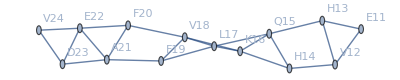

```mathematica
PDBTabulateDARRContratsIntra[MolList[[1]],IgnoreAdjacent->0,OutputStyle->"Graph"]
```

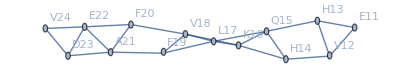

-Graphics-

```mathematica
ContactListIntra=PDBTabulateDARRContratsIntra[MolList[[1]],IgnoreAdjacent->0,SameTypeAAContact->True]
```

{E11\V12,E11\H13,V12\H13,V12\H14,H13\H14,H13\Q15,H14\Q15,H14\K16,Q15\K16,Q15\L17,K16\L17,K16\V18,L17\V18,L17\F19,V18\F19,V18\F20,F19\F20,F19\A21,F20\A21,F20\E22,A21\E22,A21\D23,E22\D23,E22\V24,D23\V24}

```mathematica
PDBTabulateDARRContratsIntra[MolList[[1]],IgnoreAdjacent->0,SameTypeAAContact->True,OutputStyle->"Distances"]
```

E11\V12
E11CA
E11CB
E11CG
E11CD
E11C | V12CA
3.8614
4.51732
5.86432
No Cnt
2.53144 | V12CB
4.6039
5.58927
6.94582
No Cnt
3.28842 | V12CG1
4.93702
6.10536
No Cnt
No Cnt
3.96276 | V12CG2
6.02459
6.90001
No Cnt
No Cnt
4.61216 | V12C
4.73467
5.16
6.29639
No Cnt
3.67907 |  |  |  | 
E11\H13
E11CA
E11CB
E11CG
E11CD
E11C | H13CA
No Cnt
No Cnt
No Cnt
No Cnt
6.01721 | H13CB
No Cnt
6.9142
No Cnt
No Cnt
6.24753 | H13CG
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H13CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H13CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H13C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt |  |  | 
V12\H13
V12CA
V12CB
V12CG1
V12CG2
V12C | H13CA
3.82466
4.60195
5.16432
4.49875
2.5193 | H13CB
4.46863
5.5685
6.28366
5.61273
3.29241 | H13CG
5.94867
6.97489
No Cnt
6.90619
4.68741 | H13CE1
No Cnt
No Cnt
No Cnt
No Cnt
6.54886 | H13CD2
6.9676
No Cnt
No Cnt
No Cnt
5.83971 | H13C
4.74392
5.20821
5.82909
4.64418
3.67116 |  |  | 
V12\H14
V12CA
V12CB
V12CG1
V12CG2
V12C | H14CA
No Cnt
No Cnt
No Cnt
6.37991
5.98283 | H14CB
No Cnt
No Cnt
No Cnt
6.00782
6.30055 | H14CG
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H14CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H14CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | H14C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt |  |  | 
H13\H14
H13CA
H13CB
H13CG
H13CE1
H13CD2
H13C | H14CA
3.81594
4.56602
4.24919
4.6027
4.70852
2.4443 | H14CB
4.57485
5.62442
5.57791
6.05676
6.14521
3.20221 | H14CG
5.99777
6.92937
6.74671
No Cnt
No Cnt
4.55436 | H14CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.43469 | H14CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
5.73408 | H14C
4.82232
5.35106
4.62773
4.23804
4.91507
3.67137 |  |  | 
H13\Q15
H13CA
H13CB
H13CG
H13CE1
H13CD2
H13C | Q15CA
No Cnt
No Cnt
6.23692
5.26416
6.04698
5.88722 | Q15CB
No Cnt
No Cnt
6.01592
4.72961
5.56299
6.36839 | Q15CG
No Cnt
No Cnt
No Cnt
5.77715
6.81972
No Cnt | Q15CD
No Cnt
No Cnt
No Cnt
5.76119
6.81395
No Cnt | Q15C
No Cnt
No Cnt
No Cnt
6.74558
No Cnt
6.94006 |  |  |  | 
H14\Q15
H14CA
H14CB
H14CG
H14CE1
H14CD2
H14C | Q15CA
3.73215
4.50107
4.15387
4.44594
4.68191
2.4416 | Q15CB
4.60077
5.66584
5.50984
5.78974
6.16575
3.35219 | Q15CG
6.03747
No Cnt
6.71413
6.73739
No Cnt
4.68526 | Q15CD
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
5.74671 | Q15C
4.64427
5.05587
4.2493
3.77267
4.5237
3.59036 |  |  |  | 
H14\K16
H14CA
H14CB
H14CG
H14CE1
H14CD2
H14C | K16CA
6.94241
No Cnt
5.989
4.87025
5.77073
5.87512 | K16CB
6.99967
6.79511
5.53413
4.17645
5.02644
6.12644 | K16CG
No Cnt
No Cnt
6.67401
5.00476
6.0674
No Cnt | K16CD
No Cnt
No Cnt
6.5895
4.86966
5.75744
No Cnt | K16CE
No Cnt
No Cnt
No Cnt
6.22166
No Cnt
No Cnt | K16C
No Cnt
No Cnt
No Cnt
6.30732
6.98244
6.90546 |  |  | 
Q15\K16
Q15CA
Q15CB
Q15CG
Q15CD
Q15C | K16CA
3.80009
4.49078
4.16271
5.50788
2.45953 | K16CB
4.50552
5.53576
5.4687
6.89479
3.13841 | K16CG
5.96216
6.91008
6.74175
No Cnt
4.52301 | K16CD
6.79002
No Cnt
No Cnt
No Cnt
5.43108 | K16CE
No Cnt
No Cnt
No Cnt
No Cnt
6.8141 | K16C
4.75403
5.20005
4.4495
5.61101
3.67624 |  |  | 
Q15\L17
Q15CA
Q15CB
Q15CG
Q15CD
Q15C | L17CA
6.97109
No Cnt
6.00226
6.74691
5.97899 | L17CB
No Cnt
6.87225
5.56602
5.98774
6.28781 | L17CG
No Cnt
6.82041
5.53681
5.75398
6.40889 | L17CD1
No Cnt
No Cnt
6.78207
6.74904
No Cnt | L17CD2
6.38693
5.7433
4.43817
4.4323
5.79371 | L17C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt |  |  | 
K16\L17
K16CA
K16CB
K16CG
K16CD
K16CE
K16C | L17CA
3.81007
4.59737
4.55485
5.88664
6.22912
2.42383 | L17CB
4.51413
5.62248
5.80253
No Cnt
No Cnt
3.2126 | L17CG
4.85603
6.09895
6.23281
No Cnt
No Cnt
3.90254 | L17CD1
6.37738
No Cnt
No Cnt
No Cnt
No Cnt
5.36276 | L17CD2
4.8118
6.24436
6.66786
No Cnt
No Cnt
4.1703 | L17C
4.75634
5.27105
4.77438
5.98484
5.94973
3.5776 |  |  | 
K16\V18
K16CA
K16CB
K16CG
K16CD
K16CE
K16C | V18CA
No Cnt
No Cnt
6.49091
No Cnt
6.85816
5.92535 | V18CB
No Cnt
No Cnt
6.08786
6.68356
5.93602
6.22432 | V18CG1
No Cnt
No Cnt
6.14637
6.57159
5.91013
6.22373 | V18CG2
No Cnt
No Cnt
No Cnt
No Cnt
6.68794
No Cnt | V18C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt |  |  |  | 
L17\V18
L17CA
L17CB
L17CG
L17CD1
L17CD2
L17C | V18CA
3.85268
4.62673
5.20732
5.26173
6.70053
2.47154 | V18CB
4.57681
5.66678
6.3062
6.58169
No Cnt
3.22498 | V18CG1
4.76834
5.96429
6.90895
No Cnt
No Cnt
3.76005 | V18CG2
6.01154
No Cnt
No Cnt
No Cnt
No Cnt
4.57464 | V18C
4.93186
5.42255
6.02561
5.7428
No Cnt
3.73147 |  |  |  | 
L17\F19
L17CA
L17CB
L17CG
L17CD1
L17CD2
L17C | F19CA
No Cnt
No Cnt
No Cnt
6.95422
No Cnt
5.98543 | F19CB
No Cnt
No Cnt
No Cnt
6.56495
No Cnt
6.38989 | F19CG
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CD1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CZ
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CE2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
V18\F19
V18CA
V18CB
V18CG1
V18CG2
V18C | F19CA
3.83821
4.62178
5.36049
4.26377
2.54572 | F19CB
4.59927
5.57849
6.52852
5.2507
3.55598 | F19CG
6.02153
6.99687
No Cnt
6.6181
4.83398 | F19CD1
6.48648
No Cnt
No Cnt
No Cnt
5.20672 | F19CE1
No Cnt
No Cnt
No Cnt
No Cnt
6.46641 | F19CZ
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CE2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F19CD2
No Cnt
No Cnt
No Cnt
No Cnt
5.90461 | F19C
4.71831
5.086
5.80133
4.28485
3.55779
V18\F20
V18CA
V18CB
V18CG1
V18CG2
V18C | F20CA
No Cnt
No Cnt
No Cnt
6.28802
5.92753 | F20CB
No Cnt
No Cnt
No Cnt
6.20135
6.30089 | F20CG
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20CD1
No Cnt
No Cnt
No Cnt
6.83769
No Cnt | F20CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20CZ
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20CE2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
F19\F20
F19CA
F19CB
F19CG
F19CD1
F19CE1
F19CZ
F19CE2
F19CD2
F19C | F20CA
3.85584
4.46446
4.23356
5.02593
5.29767
4.93322
4.18431
3.70816
2.52139 | F20CB
4.70282
5.61662
5.60295
6.3352
6.63086
6.34351
5.68059
5.20386
3.31286 | F20CG
6.00551
6.76258
6.68543
No Cnt
No Cnt
No Cnt
6.40177
6.04549
4.52821 | F20CD1
6.30104
6.96842
No Cnt
No Cnt
No Cnt
No Cnt
6.95075
6.41965
4.77829 | F20CE1
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.13641 | F20CZ
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt | F20CE2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.91536 | F20CD2
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.921
5.76179 | F20C
4.80178
5.17934
4.49711
5.02425
4.87774
4.24651
3.67051
3.74095
3.73122
F19\A21
F19CA
F19CB
F19CG
F19CD1
F19CE1
F19CZ
F19CE2
F19CD2
F19C | A21CA
No Cnt
No Cnt
6.08749
6.47519
5.88241
4.78215
4.27994
4.98829
6.05051 | A21CB
No Cnt
6.94145
5.69675
5.87208
5.03639
3.79295
3.5313
4.59607
6.41981 | A21C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.09011
5.41953
6.06266
No Cnt |  |  |  |  |  | 
F20\A21
F20CA
F20CB
F20CG
F20CD1
F20CE1
F20CZ
F20CE2
F20CD2
F20C | A21CA
3.83861
4.55039
4.43125
5.34015
5.90071
5.63018
4.76558
4.16354
2.46291 | A21CB
4.61816
5.62151
5.75661
6.6281
No Cnt
No Cnt
6.29255
5.6375
3.20822 | A21C
4.73125
5.22272
4.65718
5.33424
5.53307
5.0338
4.29249
4.15632
3.61299 |  |  |  |  |  | 
F20\E22
F20CA
F20CB
F20CG
F20CD1
F20CE1
F20CZ
F20CE2
F20CD2
F20C | E22CA
6.90562
No Cnt
6.0895
6.67844
6.40581
5.41027
4.64619
5.11175
5.86951 | E22CB
No Cnt
6.86351
5.73839
6.22764
5.72604
4.52617
3.80811
4.59646
6.27338 | E22CG
No Cnt
No Cnt
6.84848
No Cnt
6.35217
5.08687
4.69316
5.73909
No Cnt | E22CD
No Cnt
No Cnt
No Cnt
No Cnt
6.43037
5.33118
5.26628
6.35033
No Cnt | E22C
No Cnt
No Cnt
No Cnt
No Cnt
No Cnt
6.84977
5.9936
6.38835
6.90157 |  |  |  | 
A21\E22
A21CA
A21CB
A21C | E22CA
3.83549
4.77475
2.5319 | E22CB
4.68743
5.89085
3.44768 | E22CG
6.10535
No Cnt
4.7503 | E22CD
6.43147
No Cnt
4.9488 | E22C
4.67961
5.30023
3.61263 |  |  |  | 
A21\D23
A21CA
A21CB
A21C | D23CA
6.90606
No Cnt
5.86992 | D23CB
No Cnt
No Cnt
6.36334 | D23CG
No Cnt
No Cnt
6.63068 | D23C
No Cnt
No Cnt
6.99651 |  |  |  |  | 
E22\D23
E22CA
E22CB
E22CG
E22CD
E22C | D23CA
3.8377
4.63194
4.64533
5.00262
2.4731 | D23CB
4.77762
5.83947
5.96029
6.09974
3.47307 | D23CG
5.21966
6.31285
6.26973
6.03294
4.22541 | D23C
4.71206
5.13116
4.68623
4.96397
3.55114 |  |  |  |  | 
E22\V24
E22CA
E22CB
E22CG
E22CD
E22C | V24CA
6.91656
6.99334
6.25947
6.62579
5.79986 | V24CB
No Cnt
6.83933
5.96935
6.51179
6.14568 | V24CG1
No Cnt
No Cnt
6.58311
No Cnt
6.53911 | V24CG2
No Cnt
No Cnt
6.79779
No Cnt
No Cnt | V24C
No Cnt
No Cnt
No Cnt
No Cnt
6.9995 |  |  |  | 
D23\V24
D23CA
D23CB
D23CG
D23C | V24CA
3.85272
4.59544
5.14068
2.46953 | V24CB
4.69249
5.73947
6.36062
3.35449 | V24CG1
5.27245
6.34927
No Cnt
4.21217 | V24CG2
6.00861
6.98199
No Cnt
4.56273 | V24C
4.83179
5.2225
5.77153
3.63699 |  |  |  |

```mathematica
Options[PDBTabulateDARRContratsIntra]
```

{IgnoreAdjacent→1,DARRNuclearRegx→^C.*$,OutputStyle→Contacts,SameTypeAAContact→False}

### Inter-molecular contacts

```mathematica
PDBTabulateDARRContratsInter[MolList[[1]],MolList[[2]],SameTypeAAContact->True,OutputStyle->"Contacts"]
```

Chain 1:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

Chain 2:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

{H13\E11-2,H13\V12-2,H14\E11-2,H14\V12-2,H14\H13-2,Q15\E11-2,Q15\V12-2,Q15\H13-2,K16\V12-2,K16\H13-2,K16\H14-2,L17\V12-2,L17\H13-2,L17\H14-2,L17\Q15-2,V18\H14-2,V18\Q15-2,V18\K16-2,V18\L17-2,F19\Q15-2,F19\K16-2,F19\L17-2,F19\V18-2,F20\K16-2,F20\L17-2,F20\V18-2,F20\F19-2,A21\L17-2,A21\V18-2,A21\F19-2,A21\F20-2,E22\V18-2,E22\F19-2,E22\F20-2,D23\F19-2,D23\F20-2,D23\A21-2,V24\F19-2,V24\F20-2,V24\A21-2,V24\E22-2,V24\D23-2}

Chain 1:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

Chain 2:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

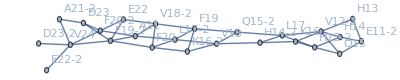

```mathematica
PDBTabulateDARRContratsInter[MolList[[1]],MolList[[2]],SameTypeAAContact->True,OutputStyle->"Graph"]
```

```mathematica
Options[PDBTabulateDARRContratsInter]
```

{DARRNuclearRegx→^C.*$,OutputStyle→Contacts,SameTypeAAContact→False}

```mathematica
contactListInter=PDBTabulateDARRContratsInter[MolList[[1]],MolList[[2]],SameTypeAAContact->True,OutputStyle->"Contacts"]
```

Chain 1:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

Chain 2:E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24,

{H13\E11-2,H13\V12-2,H14\E11-2,H14\V12-2,H14\H13-2,Q15\E11-2,Q15\V12-2,Q15\H13-2,K16\V12-2,K16\H13-2,K16\H14-2,L17\V12-2,L17\H13-2,L17\H14-2,L17\Q15-2,V18\H14-2,V18\Q15-2,V18\K16-2,V18\L17-2,F19\Q15-2,F19\K16-2,F19\L17-2,F19\V18-2,F20\K16-2,F20\L17-2,F20\V18-2,F20\F19-2,A21\L17-2,A21\V18-2,A21\F19-2,A21\F20-2,E22\V18-2,E22\F19-2,E22\F20-2,D23\F19-2,D23\F20-2,D23\A21-2,V24\F19-2,V24\F20-2,V24\A21-2,V24\E22-2,V24\D23-2}

### Binary contact chart

```mathematica
AAlist=PDBResidueSeq[MolList[[1]],ReturnSeqOnly->True]
```

{E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24}

```mathematica
Options[ContactChartSymmetric]//InputForm
```

{ContactSymbol -> Item[Graphics[{}, Background -> RGBColor[1, 0, 0], ImageSize -> {50, 50}], Background -> RGBColor[1, 0, 0]], 
 NonContactSymbol -> Item[Graphics[{}, Background -> GrayLevel[1], ImageSize -> {50, 50}], Background -> GrayLevel[1]]}

```mathematica
Options[ContactChartSymmetric]
```

{ContactSymbol→-Graphics-,NonContactSymbol→-Graphics-}

```mathematica
exampleContactChart1=ContactChartSymmetric[AAlist,ContactListIntra]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*export into svg files*)Export[NotebookDirectory[]<>"rs3.svg",exampleContactChart1]
```

C:\Users\ygao350\Dropbox\MathematicaConfig\YG\Examples\rs3.svg

```mathematica
ContactChartDistanceIntra[MolList[[1]]]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Inter-molecular contact chart (list of residue sequence,)

An important step: Convert the inter-molecular contact list into the intra-molecular format. Remove the last “-2” string.

```mathematica
contactListInterFix=StringDrop[#,-2]&/@contactListInter
```

{H13\E11,H13\V12,H14\E11,H14\V12,H14\H13,Q15\E11,Q15\V12,Q15\H13,K16\V12,K16\H13,K16\H14,L17\V12,L17\H13,L17\H14,L17\Q15,V18\H14,V18\Q15,V18\K16,V18\L17,F19\Q15,F19\K16,F19\L17,F19\V18,F20\K16,F20\L17,F20\V18,F20\F19,A21\L17,A21\V18,A21\F19,A21\F20,E22\V18,E22\F19,E22\F20,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,V24\D23}

```mathematica
ContactChartAsymmetric2Peptides[AAlist,AAlist,contactListInterFix]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
contactListInterFix
```

{H13\E11,H13\V12,H14\E11,H14\V12,H14\H13,Q15\E11,Q15\V12,Q15\H13,K16\V12,K16\H13,K16\H14,L17\V12,L17\H13,L17\H14,L17\Q15,V18\H14,V18\Q15,V18\K16,V18\L17,F19\Q15,F19\K16,F19\L17,F19\V18,F20\K16,F20\L17,F20\V18,F20\F19,A21\L17,A21\V18,A21\F19,A21\F20,E22\V18,E22\F19,E22\F20,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,V24\D23}

```mathematica
ContactChartSymmetric[AAlist,contactListInterFix]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## If you just want to have a general binary contact chart, you can do it in this way: (You don’t need to regroup any molecules)

#### 1. Load PDB file. 2. Generate the Residue sequence

```mathematica
AAlist=PDBResidueSeq[PDBDataList,ReturnSeqOnly->True]
```

{E11,V12,H13,H14,Q15,K16,L17,V18,F19,F20,A21,E22,D23,V24}

#### 3. Full contact list for one PDB file (all the contacts)

```mathematica
Options[PDBTabulateDARRContratsFull]
```

{IgnoreAdjacent→1,DARRNuclearRegx→^C.*$,OutputStyle→Contacts,SameTypeAAContact→True}

```mathematica
contactListFull=PDBTabulateDARRContratsFull[PDBDataList,IgnoreAdjacent->0]
```

{E11\V12,E11\H13,V12\H13,V12\H14,H13\H14,H13\Q15,H13\E11,H13\V12,H14\Q15,H14\K16,H14\E11,H14\V12,H14\H13,Q15\K16,Q15\L17,Q15\E11,Q15\V12,Q15\H13,K16\L17,K16\V18,K16\V12,K16\H13,K16\H14,L17\V18,L17\F19,L17\V12,L17\H13,L17\H14,L17\Q15,V18\F19,V18\F20,V18\H14,V18\Q15,V18\K16,V18\L17,F19\F20,F19\A21,F19\Q15,F19\K16,F19\L17,F19\V18,F20\A21,F20\E22,F20\K16,F20\L17,F20\V18,F20\F19,A21\E22,A21\D23,A21\L17,A21\V18,A21\F19,A21\F20,E22\D23,E22\V24,E22\V18,E22\F19,E22\F20,D23\V24,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,V24\D23,V24\V18,E11\V12,E11\H13,V12\H13,V12\H14,V12\E11,H13\H14,H13\Q15,H13\E11,H13\V12,H14\Q15,H14\K16,H14\L17,H14\E11,H14\V12,H14\H13,Q15\K16,Q15\L17,Q15\E11,Q15\V12,Q15\H13,Q15\H14,K16\L17,K16\V18,K16\V12,K16\H13,K16\H14,K16\Q15,L17\V18,L17\F19,L17\V12,L17\H13,L17\H14,L17\Q15,V18\F19,V18\F20,V18\H14,V18\Q15,V18\K16,V18\L17,F19\F20,F19\A21,F19\H14,F19\Q15,F19\K16,F19\L17,F19\V18,F20\A21,F20\E22,F20\Q15,F20\K16,F20\L17,F20\V18,A21\E22,A21\D23,A21\L17,A21\V18,A21\F19,E22\D23,E22\V24,E22\V18,E22\F19,E22\F20,D23\V24,D23\V18,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,E11\V12,E11\H13,V12\H13,V12\H14,H13\H14,H13\Q15,H13\E11,H13\V12,H14\Q15,H14\K16,H14\E11,H14\V12,H14\H13,Q15\K16,Q15\L17,Q15\E11,Q15\V12,Q15\H13,K16\L17,K16\V18,K16\V12,K16\H13,K16\H14,K16\Q15,L17\V18,L17\F19,L17\V12,L17\H13,L17\H14,L17\Q15,V18\F19,V18\F20,V18\H14,V18\Q15,V18\K16,V18\L17,F19\F20,F19\A21,F19\Q15,F19\K16,F19\L17,F19\V18,F20\A21,F20\E22,F20\K16,F20\L17,F20\V18,F20\F19,A21\E22,A21\D23,A21\L17,A21\V18,A21\F19,E22\D23,E22\V24,E22\L17,E22\V18,E22\F19,E22\F20,E22\A21,D23\V24,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,V24\D23,E11\V12,E11\H13,V12\H13,V12\H14,V12\E11,H13\H14,H13\Q15,H13\E11,H14\Q15,H14\K16,H14\E11,H14\V12,H14\H13,Q15\K16,Q15\L17,Q15\E11,Q15\V12,Q15\H13,K16\L17,K16\V18,K16\V12,K16\H13,K16\H14,L17\V18,L17\F19,L17\V12,L17\H13,L17\H14,L17\Q15,V18\F19,V18\F20,V18\H14,V18\Q15,V18\K16,V18\L17,F19\F20,F19\A21,F19\H14,F19\Q15,F19\K16,F19\L17,F19\V18,F20\A21,F20\E22,F20\K16,F20\L17,F20\V18,F20\F19,A21\E22,A21\D23,A21\K16,A21\L17,A21\V18,A21\F19,E22\D23,E22\V24,E22\V18,E22\F19,E22\F20,D23\V24,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,V24\D23,E11\V12,E11\H13,V12\H13,V12\H14,V12\E11,H13\H14,H13\Q15,H13\E11,H13\V12,H14\Q15,H14\K16,H14\E11,H14\V12,H14\H13,Q15\K16,Q15\L17,Q15\E11,Q15\V12,Q15\H13,K16\L17,K16\V18,K16\V12,K16\H13,K16\H14,L17\V18,L17\F19,L17\V12,L17\H13,L17\H14,L17\Q15,V18\F19,V18\F20,V18\H14,V18\Q15,V18\K16,V18\L17,F19\F20,F19\A21,F19\Q15,F19\K16,F19\L17,F19\V18,F20\A21,F20\E22,F20\K16,F20\L17,F20\V18,F20\F19,A21\E22,A21\D23,A21\L17,A21\V18,A21\F19,E22\D23,E22\V24,E22\V18,E22\F19,E22\F20,D23\V24,D23\F19,D23\F20,D23\A21,V24\F19,V24\F20,V24\A21,V24\E22,E11\V12,E11\H13,V12\H13,V12\H14,H13\H14,H13\Q15,H14\Q15,H14\K16,Q15\K16,Q15\L17,K16\L17,K16\V18,L17\V18,L17\F19,V18\F19,V18\F20,F19\F20,F19\A21,F20\A21,F20\E22,A21\E22,A21\D23,E22\D23,E22\V24,D23\V24}

```mathematica
ContactChartSymmetric[AAlist,contactListFull]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-